```mathematica
f[x0_]:=
Module[{x=x0},
While[x>0,x=Log[x]];
x
]
```

```mathematica
f[25]
```

Log[Log[Log[Log[25]]]]

```mathematica
N[Log[Log[Log[Log[25]]]]]
```

-1.85677

# -Graphics-

```mathematica
4/Pi*∑_(p=0)^4 1/(2p+1)*Sin[2*Pi*200*(2p+1)*t]//FullSimplify//Expand
```

(4 Sin[400 π t])/π+(4 Sin[1200 π t])/(3 π)+(4 Sin[2000 π t])/(5 π)+(4 Sin[2800 π t])/(7 π)+(4 Sin[3600 π t])/(9 π)

```mathematica
NMaximize[(4 Sin[400 π t])/π+(4 Sin[1200 π t])/(3 π)+(4 Sin[2000 π t])/(5 π)+(4 Sin[2800 π t])/(7 π)+(4 Sin[3600 π t])/(9 π),{t}]
```

{1.18233,{t→-0.09275}}

```mathematica
FindMinimum[(4 Sin[400 π t])/π+(4 Sin[1200 π t])/(3 π)+(4 Sin[2000 π t])/(5 π)+(4 Sin[2800 π t])/(7 π)+(4 Sin[3600 π t])/(9 π),{{t,0}}](*0 c'est le pepart*)
```

{-1.07724,{t→-0.12175}}

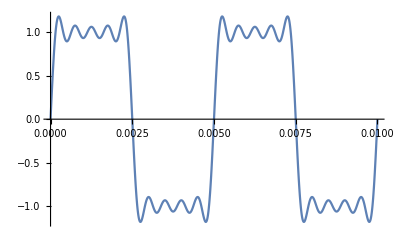

```mathematica
Plot[(4 Sin[400 π t])/π+(4 Sin[1200 π t])/(3 π)+(4 Sin[2000 π t])/(5 π)+(4 Sin[2800 π t])/(7 π)+(4 Sin[3600 π t])/(9 π),{t,0,2/200}]
```

```mathematica
(4 Sin[400 π t])/π+(4 Sin[1200 π t])/(3 π)+(4 Sin[2000 π t])/(5 π)+(4 Sin[2800 π t])/(7 π)+(4 Sin[3600 π t])/(9 π)/.t->t+1/200//FullSimplify//Expand(*T=1/200*)
```

(4 Sin[400 π t])/π+(4 Sin[1200 π t])/(3 π)+(4 Sin[2000 π t])/(5 π)+(4 Sin[2800 π t])/(7 π)+(4 Sin[3600 π t])/(9 π)

```mathematica
MaxValue[1000*Cos[2*π*10^3*t]+1250*Cos[π*10^4*t],t]
```

2250

```mathematica
MaxValue[Abs[Cos[π/2*Cos[θ]]/Sin[θ]],{θ}](*gives the maximum value offwith respect tox.*)
```

1